# Multiple Files

## Input

```mathematica
RSBfile = {"201002", "046"};
BSBfile = {"201002", "044"};
RSBfreqdet = -0.5;
RSBfreqstep = 0.1;
BSBfreqdet = -0.5;
BSBfreqstep = 0.1;
```

## Analysis

```mathematica
SetDirectory["C:\\Users\\labadmin\\Documents\\Jarvis\\data\\"];

getData[filedata_] := 
Import[filedata⟦1⟧<>"\\"<>filedata⟦2⟧<>"_PROB_"<>filedata⟦1⟧<>".csv"]
```

```mathematica
RSBdata = getData[RSBfile];
RSBprobs = RSBdata⟦3⟧/100;
BSBdata =  getData[BSBfile];
BSBprobs = BSBdata⟦3⟧/100;
```

```mathematica
RSBfreqs = Table[(RSBfreqdet + RSBfreqstep i) , {i, 0, Length[RSBprobs ]-1} ];
BSBfreqs = Table[(BSBfreqdet + BSBfreqstep i) , {i, 0, Length[BSBprobs ]-1} ];
```

## Fit

```mathematica
freqscan[x_, Ω_, ω_, A_] := Ω^2/(Ω^2 + (x-ω)^2)Sin[(√(Ω^2+(x-ω)^2)π)/(2 Ω)]^2 A
RSBfit  = NonlinearModelFit[Transpose[{RSBfreqs, RSBprobs}],{freqscan[x, Ω, ω, A], 0.1≤ A ≤ .2, 0≤ Ω≤ .2, RSBfreqdet  ≤ ω ≤ -RSBfreqdet},{{Ω,2 π 10^3}, {ω, 0}, {A,1}},x];
BSBfit  = NonlinearModelFit[Transpose[{BSBfreqs, BSBprobs}],{freqscan[x, Ω, ω, A], 0≤ A ≤ 1, 0≤ Ω≤ 10, RSBfreqdet ≤ ω ≤ -RSBfreqdet},{{Ω,1}, {ω, 0.1}, {A,0.2}},x];
```

```mathematica
RSBfit["BestFitParameters"]
RSBamp = A/.RSBfit["BestFitParameters"];
BSBamp = A/.BSBfit["BestFitParameters"];
nbar = RSBamp/BSBamp;
RSBω0 = ω/.RSBfit["BestFitParameters"];
BSBω0 = ω/.BSBfit["BestFitParameters"];
```

{Ω→0.118139,ω→0.0683563,A→0.153034}

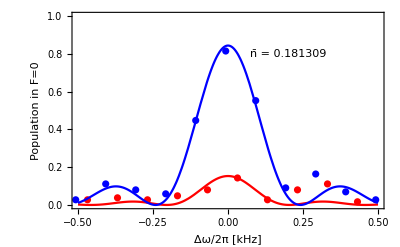

```mathematica
Show[ListPlot[Transpose[{RSBfreqs - RSBω0, RSBprobs}], PlotStyle-> Red],
Plot[RSBfit[x + RSBω0], {x, RSBfreqdet, - RSBfreqdet}, PlotStyle-> Red],
ListPlot[Transpose[{BSBfreqs - BSBω0 , BSBprobs}], PlotStyle-> Blue],
Plot[BSBfit[x + BSBω0], {x, BSBfreqdet, - BSBfreqdet}, PlotStyle-> Blue],
Epilog->{Inset[Framed[Style["n̄ = " <> ToString[nbar],12],Background->White],{-RSBfreqdet/2.5, .8}]},
PlotRange-> {{Max[RSBfreqdet, BSBfreqdet], - Max[RSBfreqdet, BSBfreqdet]},{0,1}},
Frame-> True, ImageSize-> 400, AxesOrigin-> False,FrameLabel->{{"Population in F=0",Null},{"Δω/2π [kHz]",Null}}, FrameStyle-> {Black, Bold}, LabelStyle-> {15}]
```